```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
v2mColor=Purple;
```

```mathematica
(***************************)
```

```mathematica
dateMouseSessionListV2m={{"021821","Mouse23310","Session1"},{"030221","Mouse23310","Session1"},{"031121","Mouse23310","Session1"},{"031921","Mouse23310","Session2"},{"021721","Mouse23338","Session1"},{"030221","Mouse23338","Session1"},{"031621","Mouse23338","Session1"},{"031621","Mouse23338","Session1"},{"031821","Mouse23338","Session2"},{"011721","Mouse23390","Session2"},{"011821","Mouse23390","Session2"},{"022821","Mouse23390","Session1"},{"021221","Mouse23359","Session2"},{"010321","Mouse23382","Session1"},{"010621","Mouse23382","Session2"}};
```

```mathematica
dateMouseSessionListV1toV2m={{"020421","Mouse23329","Session1"},{"021321","Mouse23329","Session1"},{"030121","Mouse23329","Session1"},{"030621","Mouse23329","Session1"},{"020421","Mouse23320","Session1"},{"121820","Mouse23365","Session1"},{"122020","Mouse23365","Session1"},{"062622","Mouse23007","Session1"}};
```

```mathematica
dateMouseSessionListLMtoV2m={{"072022","Mouse23025","Session1"},{"071222","Mouse23100","Session1"},{"071522","Mouse23100","Session1"},{"070922","Mouse23014","Session1"},{"071422","Mouse23014","Session1"},{"070922","Mouse22518","Session1"},{"071122","Mouse22518","Session1"}};
```

```mathematica
dateMouseSessionListLPtoV2m={{"010721","Mouse23339","Session1"},{"010821","Mouse23339","Session1"},{"011421","Mouse23339","Session2"},{"011221","Mouse23369","Session1"},{"011521","Mouse23369","Session1"},{"121620","Mouse23381","Session2"},{"121920","Mouse23381","Session1"},{"120920","Mouse23384","Session1"},{"121320","Mouse23384","Session1"},{"063022","Mouse23067","Session1"},{"063022","Mouse23075","Session1"},{"071022","Mouse23075","Session1"}};
```

```mathematica
(***************************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 3D****************) 
(**********************************************)
```

```mathematica
meanDFFwhiskCCV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/meanDFFwhiskCrossCorr_V1toV2m.txt","List"];
```

```mathematica
semDFFwhiskCCV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/semDFFwhiskCrossCorr_V1toV2m.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFwhiskCCLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/meanDFFwhiskCrossCorr_LPtoV2m.txt","List"];
```

```mathematica
semDFFwhiskCCLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/semDFFwhiskCrossCorr_LPtoV2m.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFwhiskCCLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/meanDFFwhiskCrossCorr_LMtoV2m.txt","List"];
```

```mathematica
semDFFwhiskCCLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/semDFFwhiskCrossCorr_LMtoV2m.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFwhiskCCV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/meanDFFwhiskCrossCorr_V2m.txt","List"];
```

```mathematica
semDFFwhiskCCV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/semDFFwhiskCrossCorr_V2m.txt","List"];
```

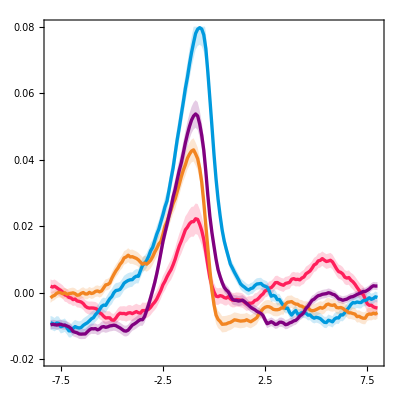

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFwhiskCCV1toV2m,Part[#,2]&/@meanDFFwhiskCCV1toV2m+(Part[#,2]&/@semDFFwhiskCCV1toV2m),Part[#,2]&/@meanDFFwhiskCCV1toV2m-(Part[#,2]&/@semDFFwhiskCCV1toV2m),Part[#,2]&/@meanDFFwhiskCCLPtoV2m,Part[#,2]&/@meanDFFwhiskCCLPtoV2m+(Part[#,2]&/@semDFFwhiskCCLPtoV2m),Part[#,2]&/@meanDFFwhiskCCLPtoV2m-(Part[#,2]&/@semDFFwhiskCCLPtoV2m),Part[#,2]&/@meanDFFwhiskCCLMtoV2m,Part[#,2]&/@meanDFFwhiskCCLMtoV2m+(Part[#,2]&/@semDFFwhiskCCLMtoV2m),Part[#,2]&/@meanDFFwhiskCCLMtoV2m-(Part[#,2]&/@semDFFwhiskCCLMtoV2m),Part[#,2]&/@meanDFFwhiskCCV2m,Part[#,2]&/@meanDFFwhiskCCV2m+(Part[#,2]&/@semDFFwhiskCCV2m),Part[#,2]&/@meanDFFwhiskCCV2m-(Part[#,2]&/@semDFFwhiskCCV2m)},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]},4->{{5},Directive[Opacity[0.2],lpColor]},4->{{6},Directive[Opacity[0.2],lpColor]},7->{{8},Directive[Opacity[0.2],lmColor]},7->{{9},Directive[Opacity[0.2],lmColor]},10->{{11},Directive[Opacity[0.2],v2mColor]},10->{{12},Directive[Opacity[0.2],v2mColor]}},PlotStyle->{{v1Color,Thickness[0.006]},Transparent,Transparent,{lpColor,Thickness[0.006]},Transparent,Transparent,{lmColor,Thickness[0.006]},Transparent,Transparent,{v2mColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.08}},FrameTicks->{{LinTicks[-0.02,0.08,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**************************************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 3E****************) 
(**********************************************)
```

```mathematica
meanDFFwhiskOnV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/meanDFFzTraceWhiskOnset_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFwhiskOnV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/semDFFzTraceWhiskOnset_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFwhiskOnLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/meanDFFzTraceWhiskOnset_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFwhiskOnLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/semDFFzTraceWhiskOnset_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFwhiskOnLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/meanDFFzTraceWhiskOnset_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFwhiskOnLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/semDFFzTraceWhiskOnset_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFwhiskOnV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/meanDFFzTraceWhiskOnset_V2m.txt","List"];
```

```mathematica
semDFFwhiskOnV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/semDFFzTraceWhiskOnset_V2m.txt","List"];
```

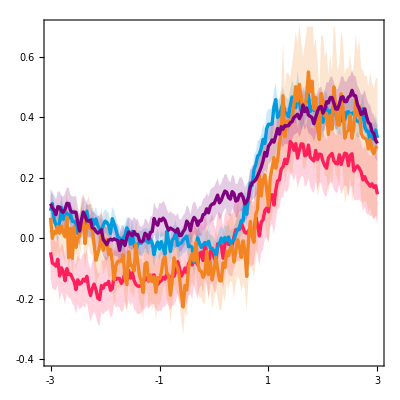

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFwhiskOnV1toV2m,Part[#,2]&/@meanDFFwhiskOnV1toV2m+(Part[#,2]&/@semDFFwhiskOnV1toV2m),Part[#,2]&/@meanDFFwhiskOnV1toV2m-(Part[#,2]&/@semDFFwhiskOnV1toV2m),Part[#,2]&/@meanDFFwhiskOnLPtoV2m,Part[#,2]&/@meanDFFwhiskOnLPtoV2m+(Part[#,2]&/@semDFFwhiskOnLPtoV2m),Part[#,2]&/@meanDFFwhiskOnLPtoV2m-(Part[#,2]&/@semDFFwhiskOnLPtoV2m),Part[#,2]&/@meanDFFwhiskOnLMtoV2m,Part[#,2]&/@meanDFFwhiskOnLMtoV2m+(Part[#,2]&/@semDFFwhiskOnLMtoV2m),Part[#,2]&/@meanDFFwhiskOnLMtoV2m-(Part[#,2]&/@semDFFwhiskOnLMtoV2m),Part[#,2]&/@meanDFFwhiskOnV2m,Part[#,2]&/@meanDFFwhiskOnV2m+(Part[#,2]&/@semDFFwhiskOnV2m),Part[#,2]&/@meanDFFwhiskOnV2m-(Part[#,2]&/@semDFFwhiskOnV2m)},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]},4->{{5},Directive[Opacity[0.2],lpColor]},4->{{6},Directive[Opacity[0.2],lpColor]},7->{{8},Directive[Opacity[0.2],lmColor]},7->{{9},Directive[Opacity[0.2],lmColor]},10->{{11},Directive[Opacity[0.2],v2mColor]},10->{{12},Directive[Opacity[0.2],v2mColor]}},PlotStyle->{{v1Color,Thickness[0.006]},Transparent,Transparent,{lpColor,Thickness[0.006]},Transparent,Transparent,{lmColor,Thickness[0.006]},Transparent,Transparent,{v2mColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-3,3},PlotRange->{{-3,3},{-0.4,0.7}},FrameTicks->{{LinTicks[-0.4,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-3,3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**************************************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 3F****************) 
(**********************************************)
```

```mathematica
peakCCValsV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/peakDFFwhiskCC_V1toV2m.txt","List"];
```

```mathematica
peakCCValsLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/peakDFFwhiskCC_LPtoV2m.txt","List"];
```

```mathematica
peakCCValsLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/peakDFFwhiskCC_LMtoV2m.txt","List"];
```

```mathematica
peakCCValsV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/peakDFFwhiskCC_V2m.txt","List"];
```

```mathematica
(**********************)
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[peakCCValsV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{-0.04,0.35}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV1toV2m,PlotRange->{All,{-0.04,0.35}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-0.04,0.35,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[peakCCValsLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{-0.04,0.35}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsLMtoV2m,PlotRange->{All,{-0.04,0.35}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-0.04,0.35,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[peakCCValsLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{-0.04,0.35}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsLPtoV2m,PlotRange->{All,{-0.04,0.35}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-0.04,0.35,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v2mAxonCharts=Show[BoxWhiskerChart[peakCCValsV2m,{{"Whiskers", Directive[Darker@v2mColor,Thick]}, {"Fences", Directive[Darker@v2mColor,Thick]},{"MedianMarker", Directive[Darker@v2mColor,Thickness[0.009]]}},PlotRange->{All,{-0.04,0.35}},ChartStyle->Directive[v2mColor,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV2m,PlotRange->{All,{-0.04,0.35}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v2mColor],Frame->False],FrameTicks->{{LinTicks[-0.04,0.35,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[peakCCValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-0.04,0.35}},ChartStyle->Transparent,Frame->False],DistributionChart[peakCCValsV2m,PlotRange->{All,{-0.04,0.35}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-0.04,0.35,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

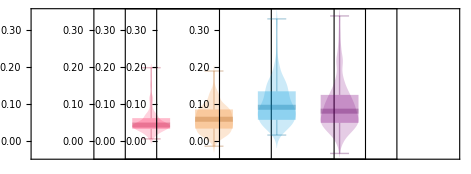

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,v2mAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}}]
```